# 2-D Barotropic Vorticity on a Rotating Sphere

## A spectral 2-D turbulence model – motivated by, but not a model of, solar convection

This notebook accompanies the Python simulation simulate_v6.py, which solves the 2-D barotropic vorticity equation on a rotating sphere with a spherical-harmonic (spectral) method. Be clear at the outset about what it is and what it is not. It is NOT a convection model: it has no buoyancy, no energy (temperature) equation, no vertical velocity, and no radial dimension. What it shares with solar convection is only the rotating-sphere geometry and the kinematics of forced two-dimensional turbulence. Solar convection appears in this notebook as motivation and as the source of that geometry; the dynamics the model actually solves are those of a single scalar vorticity field, stirred by a stochastic forcing that stands in – kinematically, not physically – for the stirring that convection would provide. Read as a self-contained tutorial: the motivating physics of solar convection, the mathematics of barotropic vorticity on a rotating sphere, the relevant dimensionless numbers, the numerics of the spectral solver, and the geometry behind the 3-D cutaway visualisation. Every code cell is standalone – evaluate them in any order.

Colour convention throughout: red = cyclonic (positive vertical vorticity), blue = anticyclonic (negative), white = zero – the same diverging map (TemperatureMap) used by the simulation's renderer.

## 1. Solar Convection — Physical Background

The Sun is a ball of plasma about 700,000 km in radius. Energy generated by hydrogen fusion in the core must escape to the surface, and it does so in two very different ways depending on depth. Below roughly 0.71 solar radii the plasma is optically thick but stable to overturning: energy diffuses outward as radiation (the radiative zone). Above 0.71 solar radii the temperature gradient becomes steep enough that the plasma is convectively unstable – hot fluid rises, cools, and sinks in a churning, turbulent layer: the convection zone.

### 1.1 Why solar convection matters

Convection is not a cosmetic surface feature; it is the engine of solar magnetism and variability:

It transports the entire solar luminosity (≈ 3.8×10^26 W) across the outer third of the Sun by radius.

Its interaction with rotation sustains the Sun's differential rotation – the equator rotates in about 25 days, the poles in about 35.

Rotating, electrically conducting convection drives the solar dynamo, producing the 11-year sunspot cycle and the magnetic activity that governs space weather.

The granulation and supergranulation patterns seen on the photosphere are the visible tops of convective cells.

### 1.2 The three key ingredients

Real solar convection is driven by buoyancy, shaped by rotation, and – in the rapidly rotating limit – constrained by the Taylor–Proudman theorem. It is worth naming these three ingredients to set the scene, but note carefully, in advance, which of them the 2-D barotropic model actually contains. Only one of the three (rotation) is present.

Buoyancy – NOT in this model. In real convection, density variations multiplied by gravity produce a buoyancy force: warm fluid is lighter and rises, cool fluid sinks. That force is what drives convection and selects its scales. The barotropic model has no temperature field, no energy equation, and no vertical velocity, so it contains no buoyancy whatsoever. In its place a stochastic forcing simply injects vorticity at chosen scales – the flow is stirred, not driven, and the “convective” scale is imposed by hand rather than selected by an instability.

Rotation – the one ingredient this model DOES keep. The Sun rotates, so the fluid feels the Coriolis force. In a 2-D model rotation enters through a single mechanism: the advection of planetary vorticity f = 2Ω sinϕ, i.e. the β-effect (Section 2.3). On the large scales relevant here, rotation is the single most important organising influence – far stronger, dynamically, than viscosity.

The Taylor–Proudman constraint – NOT in this model. In a rapidly rotating fluid the flow tends to become invariant ALONG the rotation axis, organising convection into tall columns (“banana cells”) aligned with the axis rather than isotropic blobs. This is an intrinsically THREE-dimensional balance – it constrains variation along the axis, a direction a 2-D surface model does not even possess. We derive it in Section 3 as motivating background, but a 2-D barotropic model cannot produce banana cells by this mechanism; any axis-aligned striping it shows is a property of individual spherical harmonics, not the signature of rotationally constrained convection.

### 1.3 A schematic of the solar interior

The cell below draws a labelled cross-section of the Sun's interior structure: the fusion core, the radiative zone, the thin tachocline shear layer at its top, and the turbulent convection zone reaching to the photosphere. Radii are in units of the solar radius R_⊙.

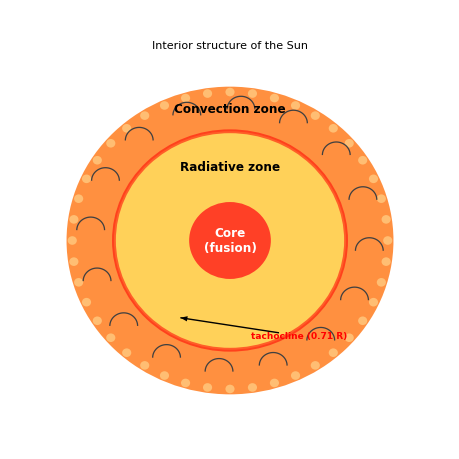

```mathematica
Module[{rCore = 0.25, rRad = 0.71, rSun = 1.0,
  granule, spokes},
 (* a little photospheric granulation on the rim *)
 granule = Table[
   {Hue[0.09, 0.55, 1], Disk[0.965 {Cos[a], Sin[a]}, 0.028]},
   {a, 0, 2 Pi - 0.01, 2 Pi/44}];
 Graphics[{
   (* convection zone *)
   {Hue[0.07, 0.75, 1.0], Disk[{0, 0}, rSun]},
   (* radiative zone *)
   {Hue[0.12, 0.65, 1.0], Disk[{0, 0}, rRad]},
   (* tachocline: thin shear layer at 0.71 R *)
   {Directive[Red, Opacity[0.55], Thickness[0.006]], Circle[{0, 0}, rRad]},
   (* fusion core *)
   {Hue[0.02, 0.85, 1.0], Disk[{0, 0}, rCore]},
   granule,
   (* convective rolls (schematic) *)
   {GrayLevel[0.25], Thickness[0.002],
    Table[Circle[(0.855) {Cos[a], Sin[a]}, 0.085, {0, Pi}],
     {a, Pi/10, 2 Pi, 2 Pi/16}]},
   (* labels *)
   Black, Thick,
   Text[Style["Core\n(fusion)", 12, White, Bold], {0, 0}],
   Text[Style["Radiative zone", 12, Black, Bold], {0, 0.48}],
   Text[Style["Convection zone", 12, Black, Bold], {0, 0.855}],
   {Red, Text[Style["tachocline (0.71 R)", 9, Bold], {0.42, -0.62}]},
   Arrow[{{0.30, -0.60}, {0.50 Cos[-3 Pi/4] + 0.05, 0.71 Sin[-3 Pi/4]/1.0 - 0.0}}]
   },
  PlotRange -> 1.15 {{-1, 1}, {-1, 1}}, ImageSize -> 460,
  PlotLabel -> Style["Interior structure of the Sun", 14, Bold]]]
```

The convective envelope occupies only the outer 29% of the Sun by radius but, because of the geometry, a substantial fraction of its volume. Our simulation models the dynamics on a representative spherical surface within this envelope.

## 2. The Mathematics

The full problem – compressible, magnetised, rotating convection in a stratified sphere – is formidable. The barotropic vorticity equation is the simplest model that still captures the essence of rotation-dominated, quasi-two-dimensional turbulence on a sphere. It describes the evolution of a single scalar field, the vertical (radial) vorticity, on a spherical surface.

### 2.1 From momentum to vorticity

Start from the momentum equation for a thin, incompressible fluid layer on a rotating sphere. Horizontal velocity u⃗ obeys

∂/(∂t)u⃗+(u⃗·∇)u⃗+f ẑ×u⃗=-1/ρ∇p+ℱ⃗

Here f = 2Ω sinϕ is the Coriolis parameter (Ω the rotation rate, ϕ latitude) and ℱ⃗ collects friction and forcing. Taking the vertical component of the curl, ẑ·∇×(·), and using incompressibility (∇·u⃗ = 0) eliminates the pressure term entirely and yields the evolution of the relative vertical vorticity ω = ẑ·∇×u⃗:

(∂ω)/(∂t)+J(ψ, ω+f)=-ν(-∇^2)^4 ω-μ ω+F

This is the equation the simulation integrates. Reading the terms left to right:

∂ω/∂t – local rate of change of vorticity.

J(ψ, ω+f) – nonlinear advection of absolute vorticity by the flow (the Jacobian, defined below). This is the term that makes the problem turbulent.

-ν (-∇×∇)^4ω – ∇^8  hyperviscosity, a scale-selective drain that only removes the very smallest scales (Section 4).

-μ ω – uniform linear (Rayleigh) drag that removes energy from the largest scales so the turbulence reaches a statistically steady state.

F – stochastic (white-in-time) forcing that injects vorticity in a chosen band of scales. It is an imposed stirring, a kinematic stand-in for the stirring convective plumes would provide; it is NOT buoyancy and does not arise from any instability. The forced scale is put in by hand through the forcing band, not selected by the dynamics.

### 2.2 Streamfunction and the vorticity–streamfunction relation

Because the horizontal flow is non-divergent, it can be written in terms of a single scalar streamfunction ψ. Velocity is the skew-gradient of ψ, and vorticity is its Laplacian:

ω=∇^2 ψ

Inverting this relation – recovering ψ from ω – is a Poisson problem, ∇^2 ψ = ω. On the sphere it is trivial in spectral space, as we will see, because spherical harmonics diagonalise the Laplacian.

### 2.3 The Coriolis parameter and planetary vorticity

The background planetary vorticity – the vorticity of the solid-body rotation of the sphere itself – is f = 2Ω sinϕ. It vanishes at the equator and is largest at the poles:

f=2 Ω sinϕ

Its gradient, the famous β = df/dy, is the restoring mechanism for Rossby waves and the reason large-scale geophysical turbulence is anisotropic. In the spectral code, f is exactly a single spherical-harmonic mode: since Y_1^0 ∝ sinϕ, the field 2Ω sinϕ is proportional to Y_1^0 alone – which is exactly how simulate_v6.py stores it. But “proportional to Y_1^0” hides a constant whose value depends entirely on the harmonic normalisation – and getting that constant wrong is exactly the bug that v5 shipped.

#### 2.3.1 A normalisation cautionary tale (the v5 Coriolis bug)

The solver (pyshtools) uses REAL, 4π-normalised spherical harmonics. In that convention the l=1, m=0 harmonic is Y_1^0 = √3 cosθ = √3 sinϕ; its peak value at the pole is √3, NOT the √(3/4π) of the more familiar orthonormal (unit-normalised) convention. To represent f = 2Ω sinϕ you need the coefficient c with c √3 sinϕ = 2Ω sinϕ, i.e. c = 2Ω/√3.

v5 instead used c = 2Ω√(4π/3) – the coefficient that is correct only for UNIT-normalised harmonics – while feeding it to 4π-normalised ones. Because the 4π-normalised harmonics are larger by a factor √(4π) ≈ 3.545, the planetary vorticity came out too large by exactly that factor. The intended Ω = 40 behaved like an effective Ω ≈ 142, and f at the pole was ≈ 283 instead of 80. v6 uses c = 2Ω/√3, giving f(pole) = 2Ω = 80 exactly. The lesson: a spectral coefficient is meaningless until you state the normalisation of the basis it multiplies.

```mathematica
With[{Ω = 40},
 Association[
  "Y10 peak (4π-norm, at pole)" -> Sqrt[3] // N,
  "v6 coefficient  2Ω/Sqrt[3]" -> 2 Ω/Sqrt[3] // N,
  "=> f(pole) = coeff*peak" -> (2 Ω/Sqrt[3]) Sqrt[3] // N,
  "v5 coefficient  2ΩSqrt[4π/3]" -> 2 Ω Sqrt[4 Pi/3] // N,
  "=> v5 effective f(pole)" -> 2 Ω Sqrt[4 Pi/3] Sqrt[3] // N,
  "overstatement factor  Sqrt[4π]" -> Sqrt[4 Pi] // N]]
(* f(pole) should be 80; v5 delivered ~283, i.e. Sqrt[4π]≈3.545x too large. *)
```

<|Y10 peak (4π-norm, at pole)→1.73205,v6 coefficient  2Ω/Sqrt[3]→46.188,=> f(pole) = coeff*peak→80.,v5 coefficient  2ΩSqrt[4π/3]→163.732,=> v5 effective f(pole)→283.593,overstatement factor  Sqrt[4π]→3.54491|>

Visualise f on the sphere. It is antisymmetric about the equator: positive (red) in the northern hemisphere, negative (blue) in the south.

```mathematica
SphericalPlot3D[1, {θ, 0, Pi}, {ϕ, 0, 2 Pi},
 ColorFunction -> Function[{x, y, z, θ, ϕ, r},
   (* f ∝ sin(latitude) = cos(θ) *)
   ColorData["TemperatureMap"][(Cos[θ] + 1)/2]],
 ColorFunctionScaling -> False, Mesh -> None, PlotPoints -> 60,
 Boxed -> False, Axes -> False, ImageSize -> 380,
 PlotLabel -> Style["Coriolis parameter  f = 2Ω sinϕ", 13, Bold]]
```

-Graphics3D-

### 2.4 Spherical harmonics as basis functions

Spherical harmonics Y_l^m(θ, ϕ) are the natural Fourier basis on the sphere. Every square-integrable field on the sphere expands as

ω(θ,ϕ)=∑_(l=0)^∞ ∑_(m=-l)^l ω_l^m Y_l^m(θ,ϕ)

with θ the colatitude and ϕ the longitude. Each harmonic factorises into an associated Legendre function in latitude and a complex exponential in longitude:

Y_l^m(θ,ϕ)=N_l^m P_l^m(cos θ) ⅇ^(ⅈ m ϕ)

The two integer indices have direct physical meaning:

The degree l sets the total horizontal wavenumber – the number of nodal circles on the sphere. Large l = small spatial scale. The characteristic angular wavelength is 2π/√(l(l+1)).

The order m sets how much of that structure is in longitude: m nodal meridians. Sectoral harmonics (m = l) are the striped, banana-like patterns aligned with the rotation axis; zonal harmonics (m = 0) are pure latitude bands.

The gallery below shows how (l, m) sets a spatial scale and shape. Large m produces elongated, axis-aligned stripes. These resemble the “banana cells” of rotating convection, but the resemblance is superficial – it is a property of the harmonic itself, not evidence that the 2-D model organises the flow this way.

```mathematica
(* each row uses valid orders m = 0, l/2, l for its degree l *)
Grid[Table[
  Table[
   SphericalPlot3D[1, {θ, 0, Pi}, {ϕ, 0, 2 Pi},
    ColorFunction -> Function[{x, y, z, θ, ϕ, r},
      ColorData["TemperatureMap"][
       Rescale[Re[SphericalHarmonicY[l, m, θ, ϕ]], {-0.45, 0.45}]]],
    ColorFunctionScaling -> False, Mesh -> None, PlotPoints -> 45,
    Boxed -> False, Axes -> False, ImageSize -> 165,
    PlotLabel -> Row[{"l=", l, ", m=", m}]],
   {m, {0, l/2, l}}],
  {l, {4, 8}}],
 Frame -> All, FrameStyle -> LightGray]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

Zonal harmonics (m = 0, left column) are pure latitude bands. As m grows toward l (right column) the pattern breaks into longitudinal stripes; the sectoral harmonics m = l are the axis-aligned bands. Rotating 3-D convection does tend to favour axis-aligned structures, but that selection is a Taylor–Proudman effect the 2-D model lacks. Here these are just basis functions, shown to build intuition for the (l, m) indexing.

### 2.5 The Jacobian: nonlinear advection, computed spectrally

The advection term is the Jacobian operator, which on the unit sphere is

J(A,B)=(∂A)/(∂ϕ)(∂B)/(∂λ)-(∂A)/(∂λ)(∂B)/(∂ϕ)

with λ longitude and ϕ latitude. Geometrically J(A, B) measures how much the contours of A and B cross: it is the rate at which the flow along contours of A advects the field B. Setting A = ψ and B = ω+f gives the advection of absolute vorticity by the streamfunction flow.

A pseudo-spectral evaluation is the standard trick and exactly what simulate_v6.py does. Products are cheap in physical (grid) space; derivatives are cheap in spectral space. So each step:

1. Transform ψ and ω+f to spectral coefficients; multiply by the appropriate wavenumbers to get the horizontal gradients.

2. Transform those gradient fields back to the grid.

3. Form the products and the difference pointwise on the grid – this is J on the grid.

4. Transform the result back to spectral space for the time step.

The forward/inverse spherical-harmonic transforms are the workhorse; everything else is elementwise arithmetic. (pyshtools performs the transforms; the code multiplies gradient components exactly as in the formula above.)

## 3. Key Dimensionless Numbers

Whether convection is rotation-dominated, and what structures it forms, is decided by a handful of dimensionless ratios. They compare the competing forces – buoyancy, rotation, viscosity, thermal diffusion – and locate the flow in parameter space.

### 3.1 The four governing numbers

Let d be the shell thickness, ΔT the superadiabatic temperature contrast, g gravity, α the thermal expansion coefficient, ν kinematic viscosity, κ thermal diffusivity, Ω the rotation rate, and U, L a characteristic velocity and length of the flow.

#### Rayleigh number – buoyancy vs diffusion

Ra=(g α ΔT d^3)/(ν κ)

The ratio of buoyant driving to the damping of viscosity and thermal diffusion. Above a critical value convection sets in; the Sun runs at Ra (≈10)^(20–24), stupendously supercritical – fully turbulent.

#### Ekman number – viscosity vs rotation

Ek=ν/(2 Ω d^2)

The ratio of viscous to Coriolis forces. The solar value is minuscule, Ek (≈10)^-15 or smaller: rotation utterly dominates viscosity. Small Ek is the hallmark of a rapidly rotating system.

#### Prandtl number – momentum vs heat diffusion

Pr=ν/κ

A property of the fluid itself. In stellar plasma Pr (≈10)^-6 (heat diffuses far faster than momentum), though most simulations, ours included, use an effective turbulent Pr of order unity.

#### Rossby number – inertia vs rotation

Ro=U/(2 Ω L)

The single most diagnostic number for the flow structure. Ro ≪ 1 means the Coriolis force dominates fluid inertia and the flow is strongly rotationally constrained. The solar convection zone has Ro ≈ 0.1–1 depending on scale: the large scales are rotationally constrained, the small granular scales are not. The model is run at high Ω (= 40 here), which does place the resolved flow at low Rossby number (Ro ≈ 0.06 at the forcing scale). But low Ro alone does not hand a 2-D model the axis-aligned columns of 3-D rotating convection – that requires the Taylor–Proudman constraint (Section 3.2), which is absent here. In practice the run stays close to isotropic, with only ~3.7% of its energy in zonal (m = 0) modes (Section 6).

### 3.2 The Taylor–Proudman theorem

Why does rapid rotation produce columns? Consider a steady, slow, inviscid flow. In the rotating frame the leading-order momentum balance is between the Coriolis force and the pressure gradient – geostrophic balance:

2 Ω⃗×u⃗=-1/ρ∇p

Take the curl of both sides. The right-hand side vanishes (the curl of a gradient is zero, for constant ρ), and with ∇·u⃗ = 0 the left side collapses to a beautifully simple statement:

(Ω⃗·∇)u⃗=0

The velocity field cannot vary along the direction of the rotation axis. If Ω⃗ points along ẑ, then ∂u⃗/∂z = 0: the flow is two-dimensional, identical on every plane perpendicular to the axis. This is the Taylor–Proudman theorem. A rotating fluid is “stiff” along the axis – it moves in rigid columns known as Taylor columns.

In a sphere, convection constrained to remain columnar wraps these columns around the inner core, producing the north–south elongated “banana cells” first described by Busse (1970). It is tempting to argue that this justifies a 2-D model: if rapid rotation makes the 3-D flow nearly two-dimensional, why not model it in 2-D directly? The argument fails on a crucial point. Taylor–Proudman makes the flow invariant ALONG the rotation axis – a direction that lies in the equatorial PLANE, not on the spherical surface this barotropic model uses. The model here evolves vorticity on a sphere; it has no axis to be stiff along and cannot represent Taylor columns at all. The derivation below is background for why rotating convection is columnar in reality – not a mechanism present in this model.

The cell below makes the constraint visible: convection columns aligned with the rotation axis, wrapping the tangent cylinder that circumscribes the inner core. This illustrates the real 3-D geometry – which the 2-D surface model does not contain.

```mathematica
Module[{axis, tanCyl, columns, sph, nCol = 14, rIn = 0.35},
 sph = {Opacity[0.08], Gray, Sphere[{0, 0, 0}, 1]};
 axis = {Thick, Black, Arrow[Tube[{{0, 0, -1.25}, {0, 0, 1.35}}, 0.006]]};
 (* tangent cylinder: circumscribes the inner core *)
 tanCyl = {Opacity[0.12], Blue,
   Cylinder[{{0, 0, -Sqrt[1 - rIn^2]}, {0, 0, Sqrt[1 - rIn^2]}}, rIn]};
 (* banana columns just outside the tangent cylinder *)
 columns = Table[
   With[{s = 0.62, a = 2 Pi k/nCol},
    {ColorData["TemperatureMap"][Mod[k, 2]], Opacity[0.85],
     Cylinder[{{s Cos[a], s Sin[a], -Sqrt[1 - s^2]},
       {s Cos[a], s Sin[a], Sqrt[1 - s^2]}}, 0.05]}],
   {k, 0, nCol - 1}];
 Graphics3D[{sph, tanCyl, columns, axis,
   Text[Style["Ω", 16, Bold], {0, 0, 1.45}]},
  Boxed -> False, ImageSize -> 400, ViewPoint -> {2.4, -1.8, 1.3},
  PlotLabel -> Style["Taylor columns aligned with the rotation axis", 13, Bold]]]
```

-Graphics3D-

### 3.3 Why rotation forces columns – a one-line scaling argument

The Taylor–Proudman result can be read as a scaling statement. Vertical variations of the flow are suppressed by a factor of the Rossby number: a structure of horizontal scale L develops vertical variation only over a height ≈ L / Ro. When Ro ≪ 1 that height exceeds the domain, so the structure spans it as a column. Rapidly rotating convection is therefore generically columnar in three dimensions. This explains why 3-D convection looks the way it does – but it is a statement about vertical (axis-parallel) structure, which the 2-D barotropic model does not represent. The simulation does NOT reproduce banana cells.

## 4. The Numerical Method

The solver is spectral: it represents ω by its spherical-harmonic coefficients ω_l^m and steps those coefficients forward in time. Two properties of spherical harmonics make this the natural choice on a sphere.

### 4.1 Spherical harmonics diagonalise the Laplacian

The single most useful fact for the whole method: spherical harmonics are eigenfunctions of the horizontal Laplacian, with eigenvalue -l(l+1) (on the unit sphere):

∇^2 Y_l^m=-l(l+1) Y_l^m

Differential operators become multiplication by numbers. Inverting the Laplacian to get the streamfunction from the vorticity – a global Poisson solve – is then a single division per mode:

ψ_l^m=-1/(l(l+1)) ω_l^m

This is the array _inv_ev in simulate_v6.py. The l = 0 mode is set to zero (a constant streamfunction carries no flow). Let us verify the eigenvalue property symbolically – apply the angular (Laplace–Beltrami) operator to Y_l^m and divide it back out:

```mathematica
angularLaplacian[f_, θ_, ϕ_] :=
  1/Sin[θ] D[Sin[θ] D[f, θ], θ] + 1/Sin[θ]^2 D[f, {ϕ, 2}];

Table[
  Simplify[
   angularLaplacian[SphericalHarmonicY[l, m, θ, ϕ], θ, ϕ] /
    SphericalHarmonicY[l, m, θ, ϕ]],
  {l, 0, 4}, {m, 0, 0}]
(* returns {0, -2, -6, -12, -20} = -l(l+1) *)
```

{{0},{-2},{-6},{-12},{-20}}

The output {0, -2, -6, -12, -20} is exactly -l(l+1) for l = 0…4. The eigenvalue depends only on l, never on m – all 2l+1 harmonics of a given degree share the same scale.

### 4.2 Hyperviscosity: ∇^8 instead of ∇^2

A real fluid dissipates through ordinary viscosity, ν∇^2 ω, whose spectral damping rate scales as l(l+1). But at the Sun's Ekman number a faithful ν would be so tiny that the smallest resolved scales, unable to dissipate, would pile up enstrophy and blow up the run. The fix is hyperviscosity: replace ∇^2  with a higher power. This solver uses ∇^8 , whose damping rate scales as [l(l+1)]^4:

damping rate(l)=μ+ν (l(l+1))^4

The key difference is selectivity. Because the exponent is so high, hyperviscosity is essentially inert across the whole inertial range and then switches on abruptly near the truncation wavenumber, cleanly absorbing the enstrophy that cascades to the grid scale while leaving the physically meaningful large and intermediate scales almost untouched. The plot compares the two, both normalised to bite at the same rate at l = 127:

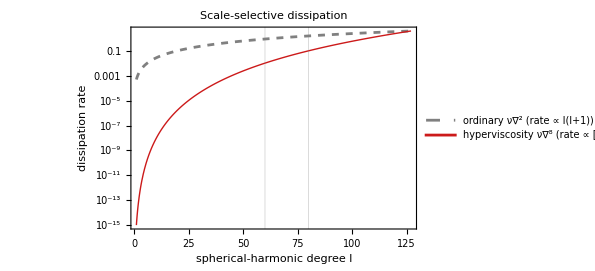

```mathematica
With[{lmax=127,mu=0.03,nu=6.*^-17,dt=0.0015},Module[{lam,hyper,ord,nuOrd},lam[l_]:=l(l+1);nuOrd=nulam[lmax]^4/lam[lmax];hyper[l_]:=nulam[l]^4;ord[l_]:=nuOrdlam[l];LogPlot[{ord[l],hyper[l]},{l,1,lmax},PlotRange->All,PlotPoints->200,PlotStyle->{{Gray,Dashed},{RGBColor[0.8,0.1,0.1],Thick}},PlotLegends->Placed[{"ordinary ν∇^2   (rate ∝ l(l+1))","hyperviscosity ν∇^8   (rate ∝ [l(l+1)]^4)"},Below],Frame->True,GridLines->{{60,80},None},FrameLabel->{"spherical-harmonic degree l","dissipation rate"},ImageSize->440,PlotLabel->Style["Scale-selective dissipation",13,Bold]]]]
```

The two vertical gridlines mark the forcing band (l = 60–80). Ordinary viscosity (dashed) already damps those forced scales appreciably; hyperviscosity (red) is orders of magnitude weaker there and only rises to meet it at the very smallest scales – preserving a broad inertial range of thin vorticity filaments. (Note the flip side, quantified in the audit section: with the forcing this close to the truncation, ~42% of the injected energy is removed by hyperviscosity at small scales instead of cascading upscale.)

### 4.3 The implicit dissipation factor and RK2 time stepping

Dissipation is handled with an integrating factor, applied as an exact multiplicative decay each step – unconditionally stable regardless of how fast the smallest scales damp:

ω_l^m=exp(-(μ+ν(l(l+1))^4)Δt) ω_l^m

The advective (nonlinear) part is advanced explicitly with a two-stage Runge–Kutta scheme (Heun's method): a predictor k_1, a corrector k_2 evaluated at the predicted state, and the average:

k_1=𝒩(ω^n)
k_2=𝒩(ω^n+Δt k_1)
ω^(n+1)=𝒟·(ω^n+Δt/2(k_1+k_2)+F)

where 𝒩 = -J(ψ, ω+f) is the advective tendency, F is the stochastic forcing added at each step, and 𝒟 is the implicit dissipation factor above. This is exactly the sequence in the step() method: two tendency evaluations, add forcing, multiply by the viscosity factor, and zero out the mean.

A word on global accuracy, to be honest about it. The advective substep is a 2nd-order Heun step and the dissipation factor is EXACT, but the two are combined by simple operator splitting (Lie–Trotter: advance advection, then apply the linear factor). Lie–Trotter splitting is only first-order accurate, so the scheme as a whole is globally O(Δt), NOT 2nd order. A step-halving test confirms it – the deterministic error ratio is 2.00, the signature of first-order convergence. For statistically steady, strongly dissipative turbulence driven by white-in-time forcing this is adequate (the strong order under such forcing is ≤ 1 regardless), but the scheme should not be advertised as 2nd-order. A Strang split, 𝒟(Δt/2)𝒩(Δt)𝒟(Δt/2), would recover 2nd order in the deterministic limit.

### 4.4 Stochastic forcing as a proxy for buoyancy

The barotropic model has no temperature field, so there is nothing to generate buoyancy. Instead the stirring is imposed directly, by injecting random vorticity each step in a band of small scales (degrees l = 60–80 in v6), chosen to sit ABOVE the Rhines degree (measured l_R ≈ 23) so that a forward enstrophy cascade runs to smaller scales (filaments, absorbed by hyperviscosity) and SOME inverse energy transfer runs to larger scales (partly removed by the weak linear drag). The amplitude in each mode is scaled by 1/√(l(l+1)) and by √Δt so the injection behaves as a proper white-in-time forcing. After a spin-up of ~5 drag times the run reaches a statistically steady state. Note the scale separation is only marginal (l_R ≈ 23 vs forcing 60–80, ratio ~2.6), so the inverse cascade is weak and does NOT organise into jets – see Section 6 and the audit.

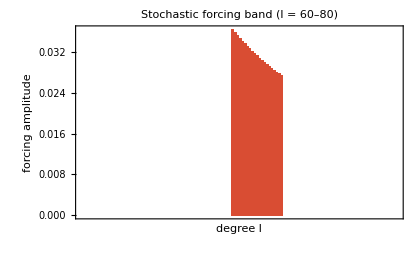

```mathematica
(* the forcing spectrum: amplitude injected per mode vs degree l *)
Module[{lmin = 60, lmax = 80, amp = 2.2},
 BarChart[
  Table[If[lmin <= l <= lmax, amp/Sqrt[l (l + 1)], 0], {l, 1, 127}],
  ChartLabels -> None, ChartStyle -> RGBColor[0.85, 0.3, 0.2],
  Frame -> True, FrameLabel -> {"degree l", "forcing amplitude"},
  PlotLabel -> Style["Stochastic forcing band (l = 60–80)", 13, Bold],
  ImageSize -> 420]]
```

## 5. Visualisation – Geometry of the Cutaway

The renderer draws a spherical shell with an octant removed so the interior is exposed. This section reconstructs the geometry in Wolfram Language so the visual choices are transparent.

### 5.1 The shell with an octant cutaway

The visualiser removes the wedge {0° ≤ longitude < 90° and latitude > 0} from the outer sphere, exposing an equatorial quarter-annulus and two meridional faces, and revealing the inner core. Here is the same geometry, with the surface coloured by a sample spherical-harmonic field to mimic the vorticity pattern.

```mathematica
Module[{outer, core, field},
 field[θ_, ϕ_] := Re[SphericalHarmonicY[8, 6, θ, ϕ]];
 outer = ParametricPlot3D[
   {Cos[ϕ] Cos[λ], Cos[ϕ] Sin[λ], Sin[ϕ]},
   {λ, 0, 2 Pi}, {ϕ, -Pi/2, Pi/2},
   RegionFunction -> Function[{x, y, z, λ, ϕ},
     Not[0 < λ < Pi/2 && z > 0]],
   ColorFunction -> Function[{x, y, z, λ, ϕ},
     ColorData["TemperatureMap"][Rescale[field[Pi/2 - ϕ, λ], {-0.4, 0.4}]]],
   ColorFunctionScaling -> False, Mesh -> None, PlotPoints -> 60,
   Boxed -> False, Axes -> False];
 core = Graphics3D[{GrayLevel[0.55], Sphere[{0, 0, 0}, 0.35]}];
 Show[outer, core, ImageSize -> 420,
  ViewPoint -> {2.2, -1.9, 1.2},
  PlotLabel -> Style["Spherical shell with octant cutaway", 13, Bold]]]
```

-Graphics3D-

### 5.2 The radial reconstruction on the cut faces

The barotropic model lives on a single spherical surface – it has no genuine radial structure. To draw a cutaway we must nonetheless say something about ω INSIDE the shell. v6 replaces v5's decorative decay with the correct RADIAL EIGENFUNCTION: each spherical-harmonic mode is continued inward by the regular solid harmonic (r/R_out)^l – the solution of Laplace's equation ∇^2(r^lY_l^m) = 0 that stays finite toward the origin, hence the natural radial structure of a harmonic scalar field. Written per mode:

ω(r,θ,ϕ)=∑_(l,m) ω_l^m (r/R_out)^l Y_l^m(θ,ϕ)

The factor (r/R_out)^l does two honest things at once. At r = R_out it equals 1, so the cut faces join the coloured surface seamlessly – no longitude shear needed. And because it decays faster the larger l is, low-l (large-scale) structures reach deep into the shell while high-l filaments stay surface-confined – the depth ordering is DERIVED from the harmonic degree, not painted on. The plot shows the weight for a few degrees; note how completely the forcing scale (l ≈ 70) dies before reaching the base at r/R = 0.71.

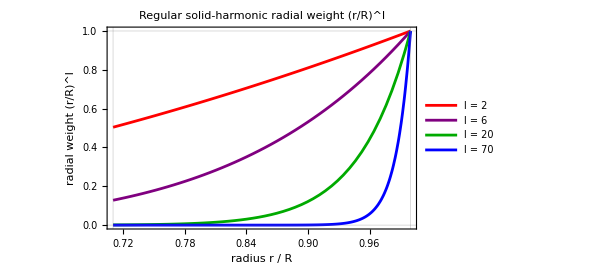

```mathematica
Module[{rIn = 0.71, rOut = 1.0, ls = {2, 6, 20, 70}},
 Plot[Evaluate[Table[(r/rOut)^l, {l, ls}]], {r, rIn, rOut},
  PlotRange -> {0, 1}, PlotStyle -> {Red, Purple, Darker[Green], Blue},
  Frame -> True, FrameLabel -> {"radius r / R", "radial weight (r/R)^l"},
  PlotLegends -> (("l = " <> ToString[#]) & /@ ls),
  GridLines -> {{rIn, rOut}, {0, 1}}, ImageSize -> 440,
  PlotLabel -> Style["Regular solid-harmonic radial weight (r/R)^l", 13, Bold]]]
```

HONESTY, as flagged in the v6 audit (§4.4): the exact (r/R)^l above puts a forcing-scale mode (l ≈ 70) at 0.71^70 ≈ 4×10^-11 of its surface amplitude at the base – i.e. the deep interior is essentially empty of small-scale structure. To fill the cutaway for display, the actual renderer (visualize_v6.py) softens the decay to (r/R)^(l/L_ref)) with L_ref ≈ 10, which OVERSTATES the penetration of forcing-scale modes by ~10× (painting l ≈ 70 at ~9% at the base). That is an illustrative choice to avoid an almost-blank interior, honestly labelled as such – a 2-D barotropic model carries no radial structure at all.

An equatorial cross-section makes the effect concrete. Taking a single longitudinal wave cos(6λ) (a stand-in for one l = 6 surface mode) and multiplying by its regular-solid-harmonic weight (r/R)^6 gives structure that is strong near the rim and decays smoothly inward – shell-following, not vertical columns. A 2-D surface field simply has no mechanism to make Taylor columns:

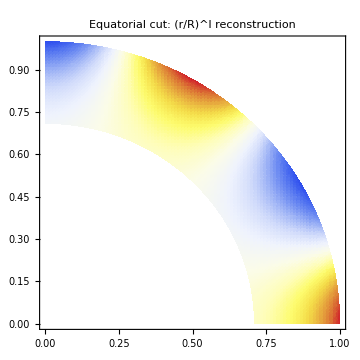

```mathematica
Module[{rIn = 0.71, rOut = 1.0, w, field},
 w[r_] := (r/rOut)^6;
 field[r_, λ_] := w[r] Cos[6 λ];
 DensityPlot[field[Sqrt[x^2 + y^2], ArcTan[x, y]],
  {x, 0, rOut}, {y, 0, rOut},
  RegionFunction -> Function[{x, y}, rIn <= Sqrt[x^2 + y^2] <= rOut],
  ColorFunction -> (ColorData["TemperatureMap"][Rescale[#, {-1, 1}]] &),
  ColorFunctionScaling -> False, PlotPoints -> 90, Mesh -> None,
  Frame -> True, AspectRatio -> 1, ImageSize -> 360,
  PlotLabel -> Style["Equatorial cut: (r/R)^l reconstruction", 13, Bold]]]
```

### 5.3 A banana-cell pattern on the sphere

Finally, a high-order sectoral harmonic (l = m) gives an axis-aligned, north–south-elongated pattern. Such patterns are the usual illustration of “banana cells” – but, as stressed throughout, the 2-D barotropic simulation does not select or reproduce them. This cell simply displays one sectoral harmonic in isolation, as a picture of what the phrase refers to.

```mathematica
SphericalPlot3D[1 + 0.06 Re[SphericalHarmonicY[12, 12, θ, ϕ]],
 {θ, 0, Pi}, {ϕ, 0, 2 Pi},
 ColorFunction -> Function[{x, y, z, θ, ϕ, r},
   ColorData["TemperatureMap"][Rescale[Re[SphericalHarmonicY[12, 12, θ, ϕ]], {-0.3, 0.3}]]],
 ColorFunctionScaling -> False, Mesh -> None, PlotPoints -> 70,
 Boxed -> False, Axes -> False, ImageSize -> 380,
 PlotLabel -> Style["Sectoral harmonic (l = m = 12): an axis-aligned pattern", 13, Bold]]
```

-Graphics3D-

## 6. Results and Discussion

### 6.1 What the simulation shows

Run at high rotation (Ω = 40, spectral truncation T127) and spun up for ~5 drag times, the model settles into a statistically steady, rotation-dominated turbulent state. The characteristic features – and, honestly, the features it was hoped for but does NOT show:

A broad, filamentary vorticity field. The spectrum genuinely broadened relative to v5 – roughly 53% of the enstrophy below / 31% in / 16% above the forcing band, versus v5's 97% trapped in-band – so a forward enstrophy cascade and some inverse transfer both exist. This is the real, measurable v6 improvement.

A broad inertial range of thin vorticity filaments, sustained by the weak, scale-selective hyperviscosity that only bites near the truncation.

A statistically steady balance: stochastic forcing injects at l = 60–80, the forward enstrophy cascade drains to small scales, and linear drag removes large-scale energy. (A caveat quantified in the audit: ~42% of the injected energy is lost to hyperviscosity at small scales rather than cascading upscale, because the forcing sits close to the dissipation range.)

NO zonal jets. The β-effect imposes some equator–pole anisotropy and Rossby-wave activity, but zonal (m = 0) energy is only ~3.7% – essentially isotropic turbulence with a whisper of anisotropy, NOT a jet regime (which would be 50–90% zonal). The scale separation that would drive jets is marginal (Rhines degree l_R ≈ 23 vs forcing 60–80), so the advertised “jets from an arrested inverse cascade” are NOT achieved at these parameters. The legitimate niche of this class of model is Jupiter-like 2-D geostrophic turbulence, which this particular run does not reach.

### 6.2 How it compares to full 3-D convection codes

Global solar-convection models such as ASH (Anelastic Spherical Harmonic; Brun & Toomre 2002) and Rayleigh (Featherstone & Hindman 2016) solve the full three-dimensional anelastic equations – momentum, energy, and often induction – on a radially resolved spherical shell. Relative to those, the barotropic model is a deliberate, extreme simplification.

The table summarises what the barotropic model keeps and what it discards.

```mathematica
Grid[{
  {Style["Feature", Bold], Style["Barotropic (this model)", Bold], Style["3-D anelastic (ASH / Rayleigh)", Bold]},
  {"Spatial dimensions", "2-D (one spherical surface)", "3-D (radially resolved shell)"},
  {"Prognostic fields", "vorticity ω only", "velocity, entropy, (magnetic field)"},
  {"Rotation / Coriolis", "yes (f = 2Ω sinϕ)", "yes (full Coriolis)"},
  {"Buoyancy driving", "none (imposed stochastic stirring)", "genuine thermal buoyancy"},
  {"Radial structure", "none (reconstructed for display)", "resolved"},
  {"Differential rotation", "not captured", "emergent"},
  {"Magnetism / dynamo", "none", "optional (MHD)"},
  {"Cost", "seconds on a laptop", "CPU/GPU-hours on a cluster"}
  },
 Frame -> All, Background -> {None, {LightYellow, None}},
 Alignment -> Left, Spacings -> {1.2, 1}, ItemSize -> {{12, 16, 18}, Automatic}]
```

Feature | Barotropic (this model) | 3-D anelastic (ASH / Rayleigh)
Spatial dimensions | 2-D (one spherical surface) | 3-D (radially resolved shell)
Prognostic fields | vorticity ω only | velocity, entropy, (magnetic field)
Rotation / Coriolis | yes (f = 2Ω sinϕ) | yes (full Coriolis)
Buoyancy driving | none (imposed stochastic stirring) | genuine thermal buoyancy
Radial structure | none (reconstructed for display) | resolved
Differential rotation | not captured | emergent
Magnetism / dynamo | none | optional (MHD)
Cost | seconds on a laptop | CPU/GPU-hours on a cluster

### 6.3 What the model gets right – and what it misses

Gets right:

Rotation-dominated 2-D dynamics. The Coriolis β-effect is represented exactly, and the resolved flow sits at low Rossby number.

The kinematics of non-divergent flow on a rotating sphere: exact vorticity–streamfunction inversion, planetary-vorticity advection, and Rossby-wave propagation.

The character of forced–dissipative 2-D turbulence: a dual cascade (forward enstrophy to filaments, some inverse energy transfer), filamentation, and a statistically steady state.

Misses:

Radial structure. There is no genuine depth dependence; the interior in the visualisation is a mapping, not a solution. Real convection has plumes spanning the depth of the zone.

Differential rotation. The solar equator-fast profile emerges from the interaction of convection, rotation, and the meridional circulation – mean flows the barotropic model cannot self-consistently generate.

Thermal physics and stratification. No temperature equation, no density stratification (which makes upflows broad and downflows narrow in the real Sun), no superadiabaticity.

Magnetism. No dynamo, hence no sunspot cycle – the phenomenon that motivates much of solar-convection research.

The barotropic model is best understood as a fast, transparent laboratory for the geometry and statistics of forced 2-D turbulence on a rotating sphere – not a model of solar convection, and (at these parameters) not even a jet-forming geostrophic-turbulence run. It is a stepping stone to, not a replacement for, the full 3-D simulations described next.

## 7. What This Model Cannot Capture

The limitations below are STRUCTURAL – they follow from the model being a single scalar equation on a 2-D surface, and no amount of parameter tuning can remove them. This is the honest boundary of what a barotropic vorticity model can say about solar convection.

No radial dimension. The model lives on one spherical surface, so it has no depth structure, no penetration or overshoot, no tachocline, and no vertical velocity – which is precisely the up/down-flow signal that convection imagery shows. The interior in the cutaway is a kinematic reconstruction (Section 5), not a solved flow.

No buoyancy or energy equation. There is no temperature, no Rayleigh number, no convective instability, and no heat transport. The flow is stirred by imposed forcing, not driven by buoyancy; the convective scale is prescribed, not selected.

No stratification or compressibility. The real Sun spans ~4–5 density scale heights, which makes upflows broad and downflows narrow; the barotropic model is incompressible and uniform.

No Taylor–Proudman constraint. This is a genuinely 3-D balance (invariance along the rotation axis), so real axis-aligned banana cells cannot arise from the correct mechanism in a 2-D surface model (Sections 1.2, 3.2).

No self-consistent differential rotation. The solar equator-fast profile emerges from correlated 3-D velocity components (Reynolds stresses, meridional circulation) that a single scalar ω cannot carry. The longitude twist on the cutaway faces is a viewing choice, not solar rotation.

No magnetism. No induction, hence no dynamo, no 11-year cycle, and no sunspots – the very phenomena that motivate much of solar-convection research. To model any of this you need a 3-D anelastic (MHD) code (see the References and README_v6.md).

## 8. The v6 Audit – What Is Verified and What Is Not

v6 is a scientifically honest rebuild of an earlier v5 run whose physics claims did not survive scrutiny. Every checkable claim was re-derived and tested numerically against the saturated field (v6_critical_audit.md). The result is a clear split between a trustworthy SOLVER and a set of claims the field does NOT support.

Verified correct (the numerics are sound):

The advection conserves energy and enstrophy to ~1×10^-6 per step in an inviscid test – the strongest single piece of evidence that the barotropic Jacobian and time step are correct.

The spherical Jacobian is metric-consistent (built from physical gradient components, avoiding the 1/cosϕ singularity) and is effectively alias-free (0.07% vs a 2×-padded reference).

The Coriolis coefficient is fixed to 2Ω/√3, giving f(pole) = 2Ω = 80 exactly (Section 2.3.1); the ∇^8 hyperviscosity, the exact integrating-factor dissipation, and the √Δt white-noise forcing scaling all check out.

Not achieved / honest caveats (properties of the run, not bugs in the solver):

Jets are NOT achieved. Zonal energy is ~3.7% – essentially isotropic turbulence. The cascade broadened (a real improvement over v5), but the marginal Rhines/forcing separation (l_R ≈ 23 vs forcing 60–80) and the ~42% energy loss to hyperviscosity keep the inverse cascade too weak to organise jets.

The time integration is globally O(Δt) (first-order Lie split of a Heun advection step with an exact linear factor), not 2nd-order – verified by a step-halving ratio of 2.00 (Section 4.3).

The interior reconstruction and the cutaway longitude twist are illustrative geometry, not solved dynamics; the display softens the true (r/R)^l decay and so overstates deep penetration of forcing-scale modes by ~10× (Section 5.2). All of this is honestly labelled in the code and captions.

## Part II — The Full Physics Programme: All Twenty Improvements

Sections 1–8 above document the v6 barotropic solver. The project has since been extended through twenty scientific improvements (scientific_improvements.md), grouped in four tiers: (A) make the barotropic model actually demonstrate the physics it claims (items 1–8 – wider scale separation, steady-state averaging, higher-order time stepping, controlled forcing, flux diagnostics); (B) extend the physics with new terms and new equation sets (items 9–14 – differential rotation, topography, deformation radius, two-layer QG, shallow water, MHD); (C) replace the model with real convection (items 15–18 – Boussinesq and anelastic shells, community solvers, Model S stratification); and (D) turn output into evidence (items 19–20 – Lagrangian FTLE, honest interior). The sections below give the governing equations, the physical meaning of each term, the numerical method, and the key references for every improvement. The implementing modules are named in each section.

Honesty note carried forward from Part I: items 1–14 all evolve a 2-D scalar field on a surface and are NOT convection – they have no buoyancy, no energy equation, no vertical velocity. Only items 15–18 add genuine convection (buoyancy + temperature + a radial dimension). Every section states plainly what it does and does not contain.

## 9. The Complete Governing Equation and Its Spectral Form

The equation the v6/v7 barotropic solver integrates, written with every term (config_v7.py, simulate_v7.py):

(∂ω)/(∂t)+J(ψ,ω+f)=-ν(-∇^2)^4 ω-μ ω+F

Reading the terms as physical processes:

∂ω/∂t – the local rate of change of the relative vertical vorticity ω = ẑ·(∇×u⃗), the single prognostic scalar of the model.

J(ψ, ω+f) – nonlinear advection of ABSOLUTE vorticity ω+f by the non-divergent flow u⃗ = ẑ×∇ψ. The advection of the PLANETARY part f by the eddies is the β-effect; it is the term that makes Rossby waves and, ultimately, jets. This nonlinearity is what makes the problem turbulent.

–ν(–∇)^2)^4ω = –ν∇^8 ω – ∇¸ hyperviscosity. In spectral space it multiplies the coefficient by –νλ)^4 with λ = l(l+1); the drain time τ = 1/(νλ)^4 is ~0.25 tu at the truncation but ~100^6 tu at the jet scale, so it removes only the smallest scales (Section 4, config_v7 NU_HYPER).

–μω – uniform linear (Rayleigh / Ekman) drag, the PRIMARY large-scale energy sink. It sets the saturated energy E_sat = ϵ/(2μ) and arrests the inverse cascade; τ_drag = 1/μ is the flow's longest memory (100 tu in v7).

F – stochastic forcing that injects vorticity in a chosen band of degrees. It is an imposed stirring, a kinematic stand-in for the convective plumes – NOT buoyancy, and not selected by any instability (see Section 11 for its statistics).

### 9.1 Vorticity–streamfunction inversion

The flow is recovered from the vorticity by inverting the Laplacian. Because the spherical harmonics diagonalise ∇.b2 (eigenvalue –l(l+1), Section 4.1), the inversion is one division per mode:

ω=∇^2 ψ⟶ψ_lm^=-ω_lm^/(l(l+1))

The equivalent-barotropic generalisation (Section 14.3) replaces the denominator l(l+1) by l(l+1)+1/L_d.b2.

### 9.2 The Jacobian in physical and spectral space

The advection operator is the Jacobian of two scalars on the sphere,

J(A,B)=ẑ·(∇A×∇B)=(ẑ×∇A)·∇B

i.e. the advection of B by the flow whose streamfunction is A. The solver evaluates it PSEUDO-SPECTRALLY and metric-consistently: transform ψ and ω+f to physical gradient components (∂θ, (1/sinθ)∂ϕ) with pyshtools, multiply on the grid to form the Jacobian, and transform back. Building it from physical gradient components (not raw ∂ϕ) avoids the 1/cosϕ pole singularity and is alias-free on the oversampled Driscoll–Healy grid (Section 8). The whole spectral update per mode is

(∂ω_lm^)/(∂t)=N_lm^(ω)-(μ+ν λ^4)ω_lm^+F_lm^,     λ=l(l+1)

with N the spectral coefficients of –J(ψ, ω+f). The linear part is diagonal (hence integrated exactly by an integrating factor or ETDRK4, Section 10); only N couples different modes.

### 9.3 The Coriolis coefficient and the √3 normalisation

The planetary vorticity f = 2Ω sinϕ is a single spherical harmonic (l=1, m=0). Its spectral coefficient depends on the normalisation of the basis, and getting it wrong was the headline v5 bug. pyshtools uses REAL, 4π-normalised harmonics, in which

Y_1^0=√3 sinϕ

so to represent f = 2Ω sinϕ the required coefficient is c with c √3 sinϕ = 2Ω sinϕ, i.e.

c_(1,0)^=(2Ω)/(√3)     ⟶     f(pole)=2Ω

The β-effect that arrests the inverse cascade is β ≡ df/dy at the equator = 2Ω on the unit sphere. (v5 used the unit-normalised coefficient 2Ω√(4π/3) with 4π-normalised harmonics, inflating f by √(4π) ≈ 3.5×; v6/v7 fix it. A spectral coefficient is meaningless until the basis normalisation is stated.)

References: Vallis (2017), Atmospheric and Oceanic Fluid Dynamics, 2nd ed. (CUP); Charney, Fjørtoft & von Neumann (1950) Tellus 2, 237.

## 10. Numerical Methods: Operator Splitting and Exponential Integrators

Improvements #3 and #4 (scientific_improvements.md §§3–4). Split the vorticity equation into a stiff LINEAR part and a nonstiff NONLINEAR part:

(∂ω)/(∂t)=L ω+N(ω),     L ω=-(μ+ν λ^4)ω,     N(ω)=-J(ψ,ω+f)

L is DIAGONAL in spectral space (it just multiplies each mode by –(μ+νλ.b3.b3... )), so its exact flow exp(Lτ) is known to machine precision – no time-step restriction from the stiff hyperviscosity. The two schemes below differ only in how they combine this exact linear flow with an explicit treatment of N.

### 10.1 Strang (2nd-order) operator splitting

v6 used a Lie–Trotter split (exact linear factor ∘ Heun advection), which is only FIRST-order globally – a verified step-halving error ratio of 2.0, and ~10% of the energy leaking anomalously to hyperviscosity. Symmetrising the composition recovers 2nd order at essentially no cost:

S(dt)=L(dt/2)·N(dt)·L(dt/2)

half-step exact linear flow ∘ full-step Heun (RK2) advection ∘ half-step exact linear flow. By the Baker–Campbell–Hausdorff expansion the leading splitting error of the ASYMMETRIC Lie product L(dt)·N(dt) is the commutator term

1/2 dt^2[L,N]+O(dt^3)

– first order globally. Symmetrising cancels that commutator, leaving –(dt.b3/24)([L,[L,N]]+2[N,[L,N]]) + …, i.e. local error O(dt.b3), global O(dt.b2). This tightens the energy/enstrophy budget and permits larger stable steps. TIME_SCHEME='strang' is the v7 default.

### 10.2 ETDRK4: exponential time differencing

Because L is diagonal, an exponential integrator treats it EXACTLY while giving 4th-order accuracy on the nonlinear Jacobian (improvement #4). ETDRK4 (Cox & Matthews 2002; Kassam & Trefethen 2005) advances one step h=dt as four Jacobian evaluations:

N_u^=N(u_n^)
a=E2·u_n^+Q·N_u^,  N_a^=N(a)
b=E2·u_n^+Q·N_a^,  N_b^=N(b)
c=E2·a+Q·(2 N_b^-N_u^),  N_c^=N(c)
u_(n+1)^=E·u_n^+N_u^f_1^+2(N_a^+N_b^)f_2^+N_c^f_3^

with the exact-linear coefficients (h=dt, z=hL per mode)

E=e^(h L),   E2=e^(h L/2),   Q=h/2 φ_1^(h L/2)

f_1^=h [-4-z+e^z(4-3z+z^2)]/z^3
f_2^=h [2+z+e^z(-2+z)]/z^3
f_3^=h [-4-3z-z^2+e^z(4-z)]/z^3

When L→0 the φ-functions reduce to E=E2=1 and the update collapses to classical RK4 – ETDRK4 is the exact-linear analogue of RK4.

### 10.3 The Kassam–Trefethen contour integral

Evaluated naively, the f_j quotients divide by z.b3, and for our modes |z|=|L·dt| ≲ 5×10^-3 – catastrophic cancellation (e^z–1)/z → 0/0 in floating point. Kassam & Trefethen (2005) average each φ-function over M points on a small circle around each eigenvalue, replacing the singular quotient by a well-conditioned Cauchy integral:

φ_j^(z)=1/(2π ⅈ)∮_γ φ_j^(t)/(t-z)ⅆt≃1/M∑_(k=1)^M φ_j^(z+r^e^(ⅈ θ_k^))

with the M=32 roots-of-unity contour (config_v7 ETDRK4_M=32). This removes the cancellation and makes the exact-linear treatment robust. ETDRK4 costs ~4 Jacobian evaluations per step vs Strang's 2 (~2× the cost) but is far more accurate on the stiff linear term – worth it at higher resolution or longer dt (TIME_SCHEME='etdrk4').

References: Strang (1968) SIAM J. Numer. Anal. 5, 506; Cox & Matthews (2002) J. Comput. Phys. 176, 430; Kassam & Trefethen (2005) SIAM J. Sci. Comput. 26, 1214; Ascher, Ruuth & Spiteri (1997) Appl. Numer. Math. 25, 151.

## 11. Physically-Grounded Stochastic Forcing

Improvement #5 (scientific_improvements.md §5). The forcing must inject a CONTROLLED energy rate ϵ in a chosen band, and optionally with a finite correlation time. config_v7 implements both.

### 11.1 Controlled energy-injection rate ϵ

Each step adds an independent Gaussian increment δω_lm to every coefficient in the band [l_min, l_max], with per-coefficient standard deviation amp_l√dt where amp_l = FORCE_AMP/√(l(l+1)). Because the increment is independent of the current field it adds enstrophy at rate amp_l.b2 and energy at rate amp_l.b2/(l(l+1)) per coefficient. Summing the (2l+1) real coefficients per degree gives the total energy-injection rate

ϵ=∑_(l=l_min^)^(l_max^) ((2l+1)amp^l^2)/(l(l+1))=FORCE_AMP^2∑_(l=l_min^)^(l_max^) (2l+1)/(l(l+1))^2

So ϵ is fixed by the amplitude and band alone; inverting lets the code set FORCE_AMP = √(ϵ_target/S_band) from a TARGET rate rather than an arbitrary amplitude (config_v7 FORCE_FROM_EPSILON). ϵ matters because it fixes the frictional-arrest / jet-spacing scale k_fr ~ (β.b3/ϵ))^(1/5) (Section 12).

### 11.2 Ornstein–Uhlenbeck coloured forcing

The 'white' branch is delta-correlated in time (a √dt Wiener increment). The 'ou' branch instead evolves a persistent forcing field f_lm with a finite correlation time τ_c as the Ornstein–Uhlenbeck process – the unique stationary Gaussian Markov process:

d f_lm^=-f_lm^/τ_c^dt+σ_l^dW

Its stationary autocovariance is the exponential

C(s)=⟨f(t) f(t+s)⟩=(σ_l^^2 τ_c^)/2 e^(-|s|/τ_c^)

with stationary variance C(0)=σ_l.b2τ_c/2 and integral time τ_c. The code implements the EXACT AR(1) discretisation of this SDE. The amplitude σ_l is fixed by demanding that as τ_c→0 the OU tendency δω=f·dt converge to the SAME white forcing (so ϵ is unchanged and the two branches are directly comparable): a tendency driven by a stationary process with ∫C ds = amp_l.b2 is white-equivalent, and for OU ∫C ds = σ_l.b2τ_c.b2, hence

σ_l^^2=amp^l/τ_c^2     ⟶     Var(f_lm^)=C(0)=amp^l/(2 τ_c^)

The field is initialised at this stationary variance (no forcing transient). Coloured forcing removes the unphysical white-noise artefact and changes the injection statistics. In BOTH branches the forcing is added AFTER the deterministic Strang/ETDRK4 substep, so its √dt scaling is preserved and it is never folded into the RK evaluations of N.

References: Maltrud & Vallis (1991) J. Fluid Mech. 228, 321; Constantinou, Farrell & Ioannou (2014) J. Atmos. Sci. 71, 1818.

## 12. Scale Analysis, Dealiasing and Cascade Diagnostics

Improvements #1, #6, #8. Together these decide whether the model demonstrably produces jets and a dual cascade – the project's stated goal.

### 12.1 The Rhines scale and the zonostrophy index

Jets emerge when the inverse energy cascade runs from the forcing scale up to the Rhines scale and is halted there by β. The Rhines wavenumber is where the eddy turnover rate matches the Rossby-wave frequency:

l_R^=√((2Ω)/U)     (β=2Ω, R=1)

with U the rms large-scale velocity. Whether jets are SHARP is measured by the zonostrophy index (Galperin, Sukoriansky et al. 2006):

R_β^=k_β^/k_R^,     k_β^=(β^3/ϵ)^(1/5),     k_R^=l_R^

Regimes: R_β ≳ 2.5 zonostrophic (sharp jets), 1.5–2.5 transitional, <1.5 friction-dominated (no jets). v6 forced at l_f≈60–80 with l_R≈23 – a separation of only 2.6, far too small, hence NO jets. v7 retunes to Ω=6.5, forcing at l=100–120, μ=0.01, giving the textbook ordering l_R(≈10) < k_β(≈26) < l_f(≈110) and a design estimate R_β≈2.6 – borderline zonostrophic. The energy balance that closes this is drag-dominated:

E_sat^=ϵ/(2μ),     U=√(ϵ/μ)

These are design targets; they must be re-measured from a saturated run (improvement #2), which is why v7 spins up for ≥5 drag times with an auto-stationarity guard (all of energy, enstrophy and zonal fraction must plateau to within 2% over a sliding window).

### 12.2 Resolution and Orszag 2/3 dealiasing

A wider inertial range needs higher truncation (improvement #6: v7 uses T170 vs v6's T127). The quadratic Jacobian generates modes up to 2L, which would alias back onto the resolved band unless removed. The Orszag (1971) 2/3 rule keeps only the lowest 2/3 of representable wavenumbers; pyshtools' Driscoll–Healy DH2 grid OVERSAMPLES (2(L+1) latitudes × 2(L+1) longitudes for degree L), so quadratic products are dealiased at this truncation – verified to 0.07% against a 2×-padded reference (Section 8).

### 12.3 Spectral flux – the direct evidence for a cascade

A broad spectrum is merely CONSISTENT with a dual cascade; it does not prove one. The rigorous diagnostic is the spectral FLUX computed from the nonlinear transfer T(l) (the projection of –J(ψ,ω+f) onto each degree; verify_v7.spectral_flux). Since Σ_l T(l)=0, the cumulative flux across degree l is

Π_E^(l)=-∑_(l_'^=1)^l T_E^(l_'^),     Π_Z^(l)=-∑_(l_'^=1)^l T_Z^(l_'^)

Π_E(l) is the net rate energy crosses from degrees ≤l to degrees >l. The dual-cascade signature that PROVES an inverse cascade is:

Π_E(l) < 0 for l BELOW the forcing band – energy flows UP-scale (toward small l): the inverse energy cascade.

Π_Z(l) > 0 for l ABOVE the forcing band – enstrophy flows DOWN-scale (toward large l): the forward enstrophy cascade.

This is the theory of Kraichnan (1967) / Batchelor: in 2-D the two quadratic invariants (energy and enstrophy) cannot both cascade the same way, so energy goes up and enstrophy goes down from the injection scale. Measuring the two flux SIGNS is what lets the project make a defensible claim about jets.

References: Rhines (1975) J. Fluid Mech. 69, 417; Vallis & Maltrud (1993) J. Phys. Oceanogr. 23, 1346; Galperin & Read (eds.), Zonal Jets (CUP 2019); Orszag (1971) J. Atmos. Sci. 28, 1074; Kraichnan (1967) Phys. Fluids 10, 1417; Boffetta & Ecke (2012) Annu. Rev. Fluid Mech. 44, 427.

## 13. Spectral Vanishing Viscosity

Improvement #7 (scientific_improvements.md §7). The ∇¸ hyperviscosity absorbs ~10% of the ENERGY (it should drain mostly enstrophy). Spectral vanishing viscosity (Tadmor 1989) is a cleaner small-scale sink: identically zero over the resolved/inertial range, switching on smoothly only near truncation. Unlike a plain Laplacian it does not damp the large scales; unlike a sharp cutoff it is smooth (no Gibbs); and being a genuine modified viscosity it supplies the entropy dissipation that guarantees convergence to the correct weak solution. It acts as a Laplacian viscosity –ϵ_SVV(l)·λω with an l-dependent coefficient (config_v7 SVV_*):

ϵ_SVV^(l)=ϵ_0^·exp[-((L-l)/(l-l_cut^))^2]     (l>l_cut^)

and ϵ_SVV(l)=0 for l≤l_cut, with L=LMAX. The kernel is 0 at l_cut, rises smoothly, and reaches ϵ_0 at the truncation. The standard cutoff is l_cut ~ √L (Maday & Tadmor 1989): √170≈13. Matching the hyperviscous cutoff rate νλ_max)^4≈4 fixes ϵ_0≈4/(170·171)≈1.4×10^-4. SVV can SUPPLEMENT ∇¸ or, with NU_HYPER=0, REPLACE it as the sole small-scale sink.

References: Tadmor (1989) SIAM J. Numer. Anal. 26, 30; Maday & Tadmor (1989) SIAM J. Numer. Anal. 26, 854; Jablonowski & Williamson (2011), in Numerical Techniques for Global Atmospheric Models (Springer).

## 14. Extended Barotropic Physics: Mean Flow, Topography, Deformation Radius

Improvements #9–#11 (scientific_improvements.md §§9–11). Three OPTIONAL extra terms in the SAME barotropic solver, disabled by default so the base run is unchanged. Each adds genuine physics with a minimal code change.

### 14.1 Differential-rotation mean flow (Newtonian relaxation)

The v6 cutaway's longitude 'shear' is a pure visualization twist, not dynamics. Instead relax the ZONAL-MEAN (m=0) vorticity toward a prescribed solar-like differential-rotation profile (Held–Suarez 1994 core), so the mean shear is a real term that can go barotropically unstable and shed eddies. A fast-equator angular velocity

Ω(ϕ)=Ω_0^-ΔΩ sin^2 ϕ

gives a zonal wind ū(ϕ) = δΩ(ϕ)·R cosϕ in the co-rotating frame (δΩ=–ΔΩ sin.b2ϕ); from ū=–(1/R)∂ψ̄/∂ϕ the target streamfunction and vorticity are

(ψ̄)_target^=(R^2 ΔΩ)/3 sin^3 ϕ,     (ω̄)_target^=∇^2 (ψ̄)_target^

applied only to the m=0 modes (∇.b2 is diagonal, so (ω̄)_target_{l0} = –l(l+1)(ψ̄)_target_{l0}). The relaxation term (Held–Suarez form) is

((∂ω̄)/(∂t)|)_relax=-1/τ_relax^(ω̄-(ω̄)_target^)

### 14.2 Topographic β / bottom relief

Add a FIXED topography h(θ,ϕ) to the potential vorticity, so the quantity advected by the flow becomes

q=ω+f+f_0^h/H≡ω+f+η

with the stationary topographic vorticity η(θ,ϕ) = f_0 h/H. The tendency –J(ψ,q) then splits as –J(ψ,ω+f) – J(ψ,η): the ONLY change is an extra advection of the fixed field η by the flow. η is an external PV source, NOT flow vorticity, so the streamfunction inversion ψ=∇)^-2ω is unchanged. Physically the stationary PV-gradient ∇η radiates topographic Rossby waves, exerts form drag, and can anchor standing eddies / lock jets – breaking the artificial zonal symmetry. In the code η is a few low-order harmonics (config_v7 TOPO_MODES, e.g. an l=2,m=0 belt + an l=3,m=2 ridge; only l≥1 is dynamical).

### 14.3 Equivalent-barotropic model: finite deformation radius

Promote the PV inversion to the free-surface / reduced-gravity form by adding one diagonal term, introducing an intrinsic length scale L_d (the Rossby radius of deformation):

q=∇^2 ψ-ψ/L_d^2(+f)

The prognostic field is now the PV anomaly q; only the inversion changes,

ψ_lm^=-q_lm^/(l(l+1)+1/L_d^2)

(was –q_lm/[l(l+1)]). With finite L_d the inverse cascade halts at L_d as well as at the Rhines scale, giving more realistic jet widths. DEFORMATION_RADIUS=None recovers the rigid-lid barotropic model byte-for-byte; L_d≈0.2 (1/L_d.b2=25, comparable to l(l+1) at l≈4–5) bites at planetary scales.

References: Held & Suarez (1994) Bull. Amer. Meteorol. Soc. 75, 1825; Vallis & Maltrud (1993) J. Phys. Oceanogr. 23, 1346; Rhines (1975) J. Fluid Mech. 69, 417; Vallis (2017) §§9, 14.

## 15. Two-Layer Quasi-Geostrophic Model (Baroclinic Instability)

Improvement #12 (two_layer_qg.py). The minimal model in which jets arise SELF-CONSISTENTLY from an internal energy source – baroclinic instability of an imposed vertical shear – rather than from ad-hoc stochastic forcing. Two layers of resting depth H_1 (upper), H_2 (lower), coupled across a density interface (reduced gravity g' = gΔρ/ρ). Each layer has a streamfunction ψ_i and a QG potential vorticity:

q_1^=∇^2 ψ_1^+f+F_1^(ψ_2^-ψ_1^),    F_1^=f_0^2/(g' H_1^)
q_2^=∇^2 ψ_2^+f+F_2^(ψ_1^-ψ_2^),    F_2^=f_0^2/(g' H_2^)

The stretching terms F_i(ψ_j–ψ_i) are vortex-stretching by the interface displacement. Each layer materially conserves its PV up to forcing/dissipation:

(∂q_1^)/(∂t)+J(ψ_1^,q_1^)=ℱ+𝒟_1^
(∂q_2^)/(∂t)+J(ψ_2^,q_2^)=𝒟_2^

### 15.1 Imposed shear as the energy source

Split each field into a fixed background + perturbation. The background is solid-body rotation Ψ_i = –U_i sinϕ (a pure Y_10). Because Ψ_i ∝ sinϕ, so is Q_i, and J(Ψ_i,Q_i)=J(sinϕ,sinϕ)=0: the background is an EXACT steady solution for any U_1,U_2. The vertical shear U_1–U_2 tilts the interface and stores available potential energy; perturbations tap it. The Charney–Stern necessary condition for instability is that the meridional PV gradient dQ_i/dϕ change sign between layers, which the F_i(U_i–U_j) term arranges once the shear exceeds a β-dependent critical value (Phillips 1954).

### 15.2 Layer coupling: 2×2 PV inversion

With ∇.b2→–λ, λ=l(l+1), the perturbation inversion q = Mψ is, per (l,m), a 2×2 system:

M=(-(λ+F_1^) | F_1^
F_2^ | -(λ+F_2^)),     det M=λ(λ+F_1^+F_2^)

so ψ=M)^-1q per mode (det=0 only at l=0, the gauge, set to zero). The coupling k_d.b2 ≡ F_1+F_2 defines the internal deformation wavenumber. Energetically, total E = Σ_i .bd H_i∫|∇ψ_i|.b2 + .bd(f_0.b2/g')∫(ψ_1–ψ_2).b2, the last term the APE; baroclinic instability converts mean APE → eddy energy → barotropic jets – the signature is barotropic KE growing at the expense of the shear.

References: Phillips (1954) Tellus 6, 273; Panetta (1993) J. Atmos. Sci. 50, 2073; Salmon, Lectures on Geophysical Fluid Dynamics (Oxford, 1998).

## 16. Rotating Shallow-Water Equations on the Sphere

Improvement #13 (shallow_water.py). Advance from one non-divergent vorticity equation to the full shallow-water system, restoring horizontal DIVERGENCE, GRAVITY WAVES and GEOSTROPHIC ADJUSTMENT – the next rung above barotropic. In vector-invariant form, for layer height h and velocity u⃗ on a unit sphere:

(∂h)/(∂t)+∇·(h u⃗)=0     (mass)
(∂u⃗)/(∂t)+(f+ζ)ẑ×u⃗+∇(Φ+K)=𝒟     (momentum)

with geopotential Φ=gh, kinetic energy K=.bd|u⃗|.b2, relative vorticity ζ=ẑ·∇×u⃗, and f=2Ωsinϕ. Taking ẑ·∇× and ∇· of the momentum equation gives a closed system for the prognostic scalars vorticity ζ, divergence δ, and height h:

(∂ζ)/(∂t)=-J(ψ,η)-∇η·∇χ-η δ
(∂δ)/(∂t)=J(η,χ)+∇η·∇ψ+η ζ-∇^2 (Φ+K)
(∂h)/(∂t)=-J(ψ,h)-∇h·∇χ-h δ

with η=ζ+f the absolute vorticity, and the velocity recovered by the Helmholtz decomposition ψ=∇)^-2ζ, χ=∇)^-2δ, u⃗=ẑ×∇ψ+∇χ. In the NON-DIVERGENT limit (δ=χ=0) the vorticity equation collapses to ∂ζ/∂t=–J(ψ,ζ+f) – the barotropic model, which the code checks. The –∇.b2Φ term and the –hδ mass term are the two sides of the gravity-wave / geostrophic-adjustment mechanism absent from barotropic.

Verification uses Williamson et al. (1992) test case 2 – global steady solid-body rotation, an exact time-independent solution (gradient-wind balance) for which all three tendencies must vanish to truncation error.

References: Williamson et al. (1992) J. Comput. Phys. 102, 211; Galewsky, Scott & Polvani (2004) Tellus A 56, 429; Bourke (1972) Mon. Wea. Rev. 100, 683.

## 17. Two-Dimensional Magnetohydrodynamics (Barotropic MHD)

Improvement #14 (mhd_barotropic.py). Add a magnetic field and the Lorentz force – the physically correct direction for the SOLAR framing, since in the tachocline a toroidal field suppresses the inverse cascade and can quench or reorganise jets. In 2-D both the velocity and the magnetic field derive from scalar potentials:

u⃗=ẑ×∇ψ,     ω=∇^2 ψ;        B⃗=ẑ×∇A,     j=∇^2 A

where A is the magnetic flux function and j the out-of-plane current density (units ρ=μ_0=1). The incompressible MHD equations reduce to TWO coupled advection equations – a vorticity equation with a Lorentz tension, and an induction equation for A:

(∂ω)/(∂t)+J(ψ,ω+f)=J(A,j)+ν∇^2 ω+F     (vorticity)
(∂A)/(∂t)+J(ψ,A)=η ∇^2 A     (induction)

with f=2Ωsinϕ, ν the (hyper)viscosity, η the magnetic diffusivity. BOTH the advection J(ψ,·) and the Lorentz tension J(A,j) use the SAME spherical Jacobian primitive – the magnetic tension is the Jacobian of the flux function with the current, exactly analogous to vorticity advection. (Sign convention: the self-consistent choice is j=∇.b2A with tension +J(A,j)=+J(A,∇.b2A), which gives σ.b2=+(k·v_A).b2>0 – restoring Alfvén waves, not a spurious instability.)

### 17.1 Ideal invariants and Alfvén waves

In the ideal limit (ν=η=F=0) 2-D MHD conserves three quadratic invariants, all checked by the code:

E=1/2∫(|u⃗|^2+|B⃗|^2)dΩ=1/2∑_lm^ λ((ψ_lm^)^2+(A_lm^)^2)
⟨A^2⟩=∑_lm^ (A_lm^)^2     (mean-square flux)
H_c^=∫u⃗·B⃗ dΩ=∑_lm^ λ ψ_lm^A_lm^     (cross-helicity)

Linearising the ideal equations about a background field B_0 gives transverse oscillations at the Alfvén frequency

ω_A^=|k⃗·OverVector[v_A]|,     OverVector[v_A]=OverVector[B_0]    (ρ=1)

ω_A ∝ |B_0| and ω_A ∝ k – the defining dispersion of Alfvén waves. The code verifies the four robust signatures: the perturbation OSCILLATES (bounded, not growing); kinetic and magnetic energy EXCHANGE periodically at fixed total; the frequency scales LINEARLY with field strength; and with the perturbation wavenumber.

References: Biskamp (2003), Magnetohydrodynamic Turbulence (CUP); Tobias, Diamond & Hughes (2007) ApJ 667, L113; Gilman (2000) ApJ 544, L79 (shallow-water MHD).

## 18. Boussinesq Rayleigh–Bénard Convection in a Rotating Shell

Improvement #15 (boussinesq_shell.py). The MINIMAL TRUE convection model. Where improvements #1–#14 all evolve a single 2-D scalar with NO buoyancy, this adds the three ingredients that make the problem convection: a temperature perturbation Θ with its own evolution equation, a BUOYANCY FORCE driving the flow, and a vertical velocity (a 3-D poloidal/toroidal field). Governing equations in a shell r_i<r<r_o, gravity g⃗=–gr̂, rotation Ωẑ, with control numbers Ra (Rayleigh), Ek (Ekman), Pr (Prandtl):

(∂Θ)/(∂t)+u⃗·∇Θ=κ∇^2 Θ+S(r)
(∂ω)/(∂t)+(u⃗·∇)ω-(ω⃗·∇)u⃗=-(2Ω)/Ek(∂u⃗)/(∂z)+Ra Pr(r̂×∇Θ)+Pr ∇^2 ω

The buoyancy term Ra·Pr·(r̂×∇Θ) is the curl of the buoyancy force ρ'g⃗∝Θr̂; the (2Ω/Ek)∂u⃗/∂z term is the curl of the Coriolis force. S(r) = –w dT̄/dr is the background heating.

### 18.1 Linear onset – the Chandrasekhar eigenvalue problem

Linearising about rest and projecting on a horizontal planform of wavenumber a, the marginal-stability amplitudes of vertical velocity W, vertical vorticity ζ and temperature Θ obey (Chandrasekhar 1961, D=d/dz, Ta=Ek)^-2 the Taylor number):

(D^2-a^2)^2 W=a^2 Ra Θ-Ta^(1/2)Dζ     (vertical momentum)
(D^2-a^2)ζ=Ta^(1/2)DW     (vertical vorticity)
(D^2-a^2)Θ=-W     (heat)

Eliminating ζ and Θ gives the sixth-order scalar eigenvalue problem whose lowest eigenvalue over the planform a is the critical Rayleigh number Ra_c:

(D^2-a^2)^3 W+Ta D^2 W=-a^2 Ra W

With fixed-temperature plates, the mechanical boundary conditions fix the classic benchmarks (solved by Chebyshev collocation, N≈40 collocation points, to machine accuracy):

Stress-free ("free"): W=D.b2W=0, Dζ=0 ⟶ Ra_c = 27π)^4/4 = 657.511 (Ta=0).

No-slip ("rigid"): W=DW=0, ζ=0 ⟶ Ra_c = 1707.762 (Ta=0).

Rapid rotation: Ra_c ∝ Ek)^(-4/3) – rotation strongly stabilises convection and selects a narrow (a∝Ek)^(-1/3)) cell, the onset of the columnar (banana-cell) regime of Section 3.2.

The convective NONLINEARITY is verified separately via the Saltzman (1962) / Lorenz (1963) Galerkin truncation – the smallest self-contained system carrying the advective nonlinearity + buoyancy exchange – which conserves energy in the dissipationless limit.

References: Chandrasekhar (1961), Hydrodynamic and Hydromagnetic Stability (Oxford); Christensen & Aubert (2006) Geophys. J. Int. 166, 97; Gastine, Wicht & Aurnou (2013) Icarus 225, 156; Saltzman (1962) J. Atmos. Sci. 19, 329; Lorenz (1963) J. Atmos. Sci. 20, 130.

## 19. Anelastic Convection in a Stratified Shell

Improvement #16 (anelastic_shell.py). Boussinesq treats the background density as uniform – valid only for a thin layer. The solar convection zone spans ~14 density scale heights (ρ varies by ~100^6 from base to photosphere), so Boussinesq is INVALID there. The anelastic approximation (Gough 1969; Braginsky & Roberts 1995) filters sound waves while retaining the strongly varying background density ρ̄(r). Its two defining consequences:

### 19.1 The anelastic mass constraint

Continuity becomes a constraint on the MASS flux, not the velocity:

∇·(ρ̄ u⃗)=0     ⟶     ∇·u⃗=-u⃗·∇ln ρ̄≠0

so the velocity itself is COMPRESSIBLE – this is what produces the up/down-flow ASYMMETRY of stratified convection: broad slow upflows, narrow fast downdrafts. The constraint is enforced exactly by writing the mass flux (not the velocity) with poloidal/toroidal scalars,

ρ̄ u⃗=∇×∇×(P r̂)+∇×(T r̂)

which makes ∇·(ρ̄u⃗) = ∇·(∇×·) ≡ 0 identically (verified to machine precision).

### 19.2 The polytropic reference state

The background is a hydrostatic polytrope over N_ρ density scale heights (Jones et al. 2011 anelastic benchmark). With aspect ratio η=r_i/r_o, polytropic index n, gravity g∝1/r.b2, the dimensionless temperature ζ(r) is linear in 1/r and the background fields are its powers:

ζ(r)=c_0^+c_1^d/r,        T̄=ζ,     ρ̄=ζ^n,     p̄=ζ^(n+1)

(d=r_o–r_i; ideal gas p̄=ρ̄T̄ automatically). Then the number of density scale heights is exactly

N_ρ^=ln[(ρ̄(r_i^))/(ρ̄(r_o^))]

and hydrostatic balance dp̄/dr = –ρ̄ḡ holds. The polytrope is p∝ρ)^((n+1)/n); it is exactly ISENTROPIC when n=n_ad=1/(γ–1) and SUPER-adiabatic (convectively unstable, ds̄/dr<0) when n<n_ad – the physical regime for convection.

References: Gough (1969) J. Atmos. Sci. 26, 448; Braginsky & Roberts (1995) GAFD 79, 1; Jones et al. (2011) Icarus 216, 120; Lantz & Fan (1999) ApJS 121, 247.

## 20. Community Solvers: Rayleigh and Dedalus

Improvement #17 (rayleigh_dedalus_setup.py). Rather than hand-build a 3-D convection solver (years of development + verification risk), map the control parameters onto a VALIDATED community code: Rayleigh (Featherstone & Hindman 2016, a pseudo-spectral anelastic convection/dynamo code) or Dedalus (Burns et al. 2020, a general spectral-PDE framework whose spherical bases express the shell system in a few dozen lines). The module emits ready-to-run input for either code from a single parameter object, with the SAME physics in both. The shared nondimensional convention:

Ra=(α g ΔT d^3)/(ν κ)     (buoyancy vs. diffusion)
Ek=ν/(2Ω d^2)     (viscosity vs. rotation)
Pr=ν/κ,     Pm=ν/η     (thermal, magnetic Prandtl)
η=r_i^/r_o^,     d=r_o^-r_i^=1     (aspect ratio)

reference_type=1 is a Boussinesq shell (improvement #15); reference_type=2 is a polytropic anelastic shell (improvement #16) parameterised by N_ρ and n. The module verifies that the Rayleigh namelist round-trips through a bundled parser (every control number reads back exactly), that the Dedalus script is valid Python whose parameter block exec's to the requested values, and that the Boussinesq↔anelastic and no-slip↔stress-free toggles propagate to both.

References: Featherstone & Hindman (2016) ApJ 818, 32 (Rayleigh); Burns, Vasil, Oishi, Lecoanet & Brown (2020) Phys. Rev. Research 2, 023068 (Dedalus); Christensen et al. (2001) Phys. Earth Planet. Inter. 128, 25 (dynamo benchmark).

## 21. Coupling to the Model S Solar Stratification

Improvement #18 (model_s_stratification.py). Drive the convection of #15–#17 with a REALISTIC solar background – temperature, density, gravity and entropy vs. radius from a standard solar model – rather than a constant or ad-hoc profile. The convective length scales, velocities and super-adiabaticity are all set by the true stratification, so Model S makes a simulation quantitatively comparable to helioseismology (0.713 ≤ r/R_⊙ ≤ 1.0). Gravity is not tabulated – the CZ holds ≲2% of the Sun's mass, so to ~1%

g(r)=(G M_⊙)/r^2,     g(r=R_⊙)=274 m s^-2

The bulk convection zone is nearly ISENTROPIC: the logarithmic gradient matches the adiabatic value,

∇=(d ln T)/(d ln P)≈∇_ad^ =(γ-1)/γ=0.4     (γ=5/3)

so ds̄/dr≈0 with only a slight super-adiabatic deficit – the small excess that actually drives the convection – departing only in the thin radiative surface layer. Anchor values the profile reproduces (Model S / standard solar model):

Base of CZ (x=0.713): T≈2.18×100^6 K, ρ≈0.187 g cm)^-3, g≈539 m s)^-2.

Photosphere (x=1.0): T≈5.77×100^3 K, ρ≈2.5×10^-7 g cm)^-3, g≈274 m s)^-2.

Density scale heights across the CZ: ln[(ρ̄)_base/(ρ̄)_top] ≈ 13.5 – the deep, highly stratified envelope that makes the ANELASTIC model (#16), not Boussinesq, the correct reduced description.

Honesty: this is a smooth fit to Model S anchored to published values, not the Model S data file itself; the thin surface ionization layers are approximate. For quantitative work, replace the bundled table with actual Model S / MESA output – the interpolant API is unchanged.

References: Christensen-Dalsgaard et al. (1996) Science 272, 1286 (Model S); Miesch (2005) Living Rev. Solar Phys. 2, 1; Stix, The Sun (2nd ed., 2002).

## 22. Lagrangian Transport and Finite-Time Lyapunov Exponents

Improvement #19 (lagrangian_ftle.py). A snapshot of vorticity is an EULERIAN object; it cannot say where fluid is stirred versus transported coherently. Advecting passive tracers with the (verified-correct) velocity field and computing FTLE extracts the Lagrangian coherent structures – the material transport BARRIERS. On a rotating sphere the zonal JETS are exactly such barriers: fluid does not cross a jet core, so an FTLE ridge sits on each jet while the flanks mix. This turns the movie into evidence about transport.

### 22.1 The tracer equation

With ψ_lm=–ω_lm/[l(l+1)] and u⃗=ẑ×∇ψ, the colatitude/longitude velocity components (unit sphere) and the tracer ODE are

u_θ=-1/sinθ(∂ψ)/(∂ϕ),     u_ϕ=(∂ψ)/(∂θ)
(∂θ)/(∂t)=u_θ,        (∂ϕ)/(∂t)=u_ϕ/sinθ

### 22.2 The flow-map gradient and FTLE

Seed a uniform grid of tracers, advect for time T under the (snapshot) field, and form the flow-map (deformation) gradient F by finite-differencing neighbouring tracers, carrying the sphere metric (arc-lengths dθ and sinθ dϕ). With σ_max the largest singular value of F (equivalently √λ_max of the right Cauchy–Green tensor C=F^TF), the FTLE is

σ_FTLE^(x)=1/(|T|)ln σ_max^(x)

Ridges of σ_FTLE are the finite-time transport barriers – and on a jet-bearing flow they trace the jet cores directly, a dynamical diagnostic no single vorticity snapshot provides.

References: Haller (2015) Annu. Rev. Fluid Mech. 47, 137 (LCS review); Shadden, Lekien & Marsden (2005) Physica D 212, 271 (FTLE ridges as LCS).

## 23. Honest Interior: the True (r/R)^l Evanescent Continuation

Improvement #20 (honest_interior.py). The v6 renderer continued the surface field inward with a mixing-length-scaled factor (r/R))^(l/L_ref) using L_ref=10, and painted the inner core ~32× amplified. Both OVERSTATE what a 2-D barotropic field can say about the deep interior. The mathematically honest continuation of a degree-l surface pattern that is regular at the origin is the interior solution of Laplace's equation:

Φ(r,θ,ϕ)=∑_lm^ (r/R)^l ω_lm^Y(θ,ϕ)

– NOT solved interior dynamics. It is EVANESCENT: high-l (small-scale) structure decays within a thin skin of depth ~R/l, while only the largest scales reach the base. The l/L_ref exponent with L_ref=10 inflates the e-folding depth by ~10×. For the forcing-scale modes (l≈60–80) the honest factor at the base r=0.71R is

(0.71)^l≈4×10^-11     (l≈60–80)

i.e. the interior is essentially EMPTY. That is the correct answer: a 2-D barotropic model carries NO radial information, so any visible interior structure is decoration, not physics. The module therefore offers the honest alternatives named in the spec: (a) show ONLY the 2-D surface field, no interior; or (b) render the TRUE (r/R)^l continuation (surface-confined for forcing-scale modes). A genuine 3-D field requires items #15–#17.

References: project audits physics_audit.md and v6_critical_audit.md §§4.4, 5.1; for a genuine 3-D field see §§15–17.

## 24. Summary: From 2-D Turbulence Toward Solar Convection

The twenty improvements trace a deliberate arc. Tier A (§§9–13) makes the barotropic model demonstrably do what it claimed: a wide forcing–Rhines separation and controlled injection aimed at the zonostrophic regime, 2nd-/4th-order time stepping with exact linear treatment, a clean spectral sink, and – decisively – a direct FLUX measurement that distinguishes a real dual cascade from a merely broadened spectrum. Tier B (§§14–17) adds genuine new physics: a self-consistent mean flow, topographic locking, a finite deformation radius, self-consistent baroclinic jets, gravity waves, and the solar-relevant Lorentz force. Tier C (§§18–21) crosses the line into ACTUAL convection – buoyancy, an energy equation, a radial dimension, correct anelastic stratification, and a real solar background. Tier D (§§22–23) converts the output from illustration into evidence and removes the one remaining misleading element.

The honest through-line: the numerics of the base solver are verified correct; the gaps were always physical SCOPE and run DISCIPLINE, not bugs. The single cheapest change with the largest scientific payoff remains items 1+2+8 together – run long enough, with wider scale separation, and MEASURE THE FLUX – which alone lets the project make a defensible claim about jets. Everything from §18 onward is the honest destination if "solar convection" is to be more than a motivating label.

## References

Busse, F. H. (1970). Thermal instabilities in rapidly rotating systems. Journal of Fluid Mechanics, 44, 441–460. [Columnar/banana-cell convection.]

Gilman, P. A. (1975). Linear simulations of Boussinesq convection in a deep rotating spherical shell. Journal of the Atmospheric Sciences, 32, 1331–1352.

Brun, A. S. & Toomre, J. (2002). Turbulent convection under the influence of rotation: sustaining a strong differential rotation. The Astrophysical Journal, 570, 865–885. [The ASH code.]

Miesch, M. S. (2005). Large-scale dynamics of the convection zone and tachocline. Living Reviews in Solar Physics, 2, 1. [Comprehensive review.]

Jones, C. A. (2011). Planetary magnetic fields and fluid dynamos. Annual Review of Fluid Mechanics, 43, 583–614. [Rotating convection and the Taylor–Proudman constraint.]

Featherstone, N. A. & Hindman, B. W. (2016). The spectral amplitude of stellar convection and its scaling in the high-Rayleigh-number regime. The Astrophysical Journal, 818, 32. [The Rayleigh code.]

Vallis, G. K. (2017). Atmospheric and Oceanic Fluid Dynamics, 2nd ed. Cambridge University Press. [Barotropic vorticity equation, geostrophic turbulence, Taylor–Proudman theorem.]

Rhines, P. B. (1975). Waves and turbulence on a beta-plane. Journal of Fluid Mechanics, 69, 417–443. [The Rhines scale and the arrest of the inverse cascade into zonal jets.]

Charney, J. G., Fjørtoft, R. & von Neumann, J. (1950). Numerical integration of the barotropic vorticity equation. Tellus, 2, 237–254. [The original barotropic-vorticity computation.]

Simulation code: config_v6.py, simulate_v6.py, visualize_v6.py – 2-D barotropic vorticity solver (pyshtools) with a 3-D spherical-shell cutaway renderer (matplotlib). Full audit in v6_critical_audit.md; overview in README_v6.md.